## 展开和变换

预备工作：

```mathematica
imgSize=300;
```

### 数项级数

#### 情形一

我们常常使用级数。那么级数如何形象的去理解呢？

举个例子说明，比如我们有一个这样的数列：

2,1/2,4/3,3/4,...,(n+(-1)^(n-1))/n,...

我们可以把这些数画在一个坐标系中。例如我们有这样一个数列：

```mathematica
exampleSeries1=(n+(-1)^(n-1))/n;
```

数列的前几项是：

```mathematica
Append[Table[exampleSeries1,{n,1,10}],"..."]
```

{2,1/2,4/3,3/4,6/5,5/6,8/7,7/8,10/9,9/10,...}

我们可以把各项在图上表示出来。其中

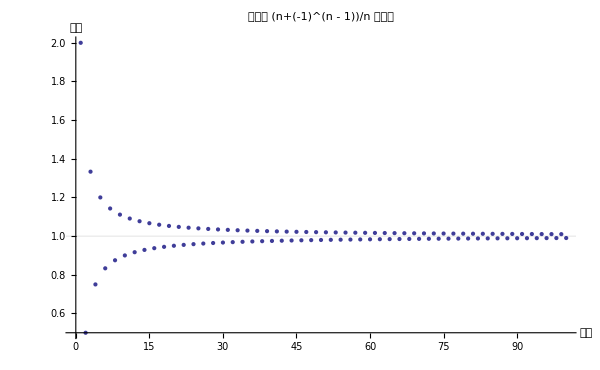
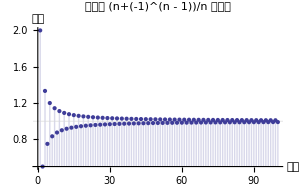
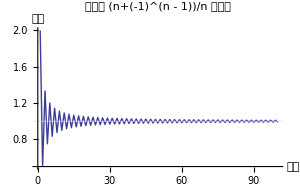

```mathematica
example1=Table[exampleSeries1,{n,1,100}];
Grid[{
{ListPlot[example1,GridLines->{{},{1}},PlotLabel->"通项为 (n+(-1)^(n - 1))/n 的数列",AxesLabel->{"项数","数列"},AxesStyle->Arrowheads[Automatic,Automatic],PlotRange->Full,ImageSize->2imgSize]},
{ListPlot[example1,Filling->Axis,GridLines->{{},{1}},PlotLabel->"通项为 (n+(-1)^(n - 1))/n 的数列",AxesLabel->{"项数","数列"},AxesStyle->Arrowheads[Automatic,Automatic],PlotRange->Full,ImageSize->imgSize]
ListPlot[example1,Joined->True,GridLines->{{},{1}},PlotLabel->"通项为 (n+(-1)^(n - 1))/n 的数列",AxesLabel->{"项数","数列"},AxesStyle->Arrowheads[Automatic,Automatic],PlotRange->Full,ImageSize->imgSize]}
}]
```

从这个图中看到这个数列的极限通项大概是越来越接近 1 的。那么它的极限到底是不是 1 呢？

```mathematica
Limit[exampleSeries,n->Infinity]
```

exampleSeries

确实是 1 。

#### 情形二

另一种情形是这样的。

```mathematica
exampleSeries2=2^-n;
```

```mathematica
Append[Table[exampleSeries2,{n,1,10}],"..."]
```

{1/2,1/4,1/8,1/16,1/32,1/64,1/128,1/256,1/512,1/1024,...}

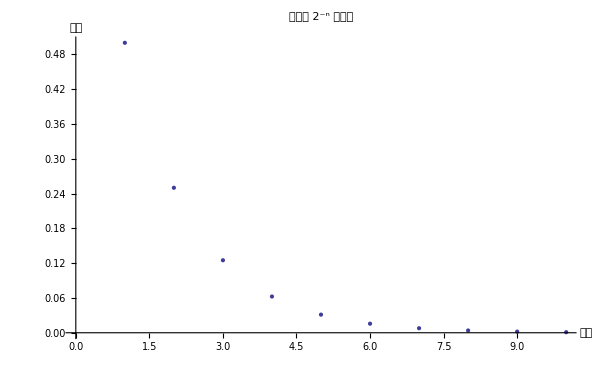
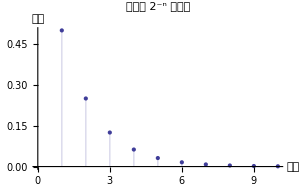
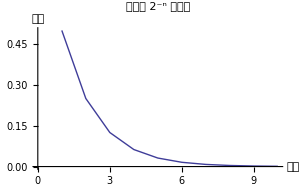

```mathematica
example2=Table[exampleSeries2,{n,1,10}];
Grid[{
{ListPlot[example2,GridLines->{{},{1}},PlotLabel->"通项为 2^-n 的数列",AxesLabel->{"项数","数列"},AxesStyle->Arrowheads[Automatic,Automatic],AxesOrigin->{0,0},PlotRange->Full,ImageSize->2imgSize]},
{ListPlot[example2,Filling->Axis,GridLines->{{},{1}},PlotLabel->"通项为 2^-n 的数列",AxesLabel->{"项数","数列"},AxesStyle->Arrowheads[Automatic,Automatic],AxesOrigin->{0,0},PlotRange->Full,ImageSize->imgSize]
ListPlot[example2,Joined->True,GridLines->{{},{1}},PlotLabel->"通项为 2^-n 的数列",AxesLabel->{"项数","数列"},AxesStyle->Arrowheads[Automatic,Automatic],AxesOrigin->{0,0},PlotRange->Full,ImageSize->imgSize]}
}]
```

#### 情形三

```mathematica
exampleSeries3=Exp[-1/n];
```

```mathematica
Append[Table[exampleSeries3,{n,1,10}],"..."]
```

{1/ⅇ,1/(√ⅇ),1/ⅇ^(1/3),1/ⅇ^(1/4),1/ⅇ^(1/5),1/ⅇ^(1/6),1/ⅇ^(1/7),1/ⅇ^(1/8),1/ⅇ^(1/9),1/ⅇ^(1/10),...}

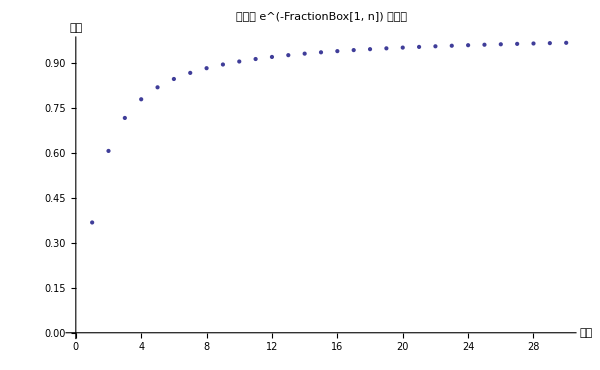
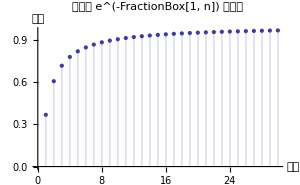
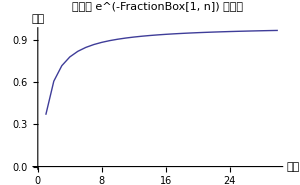

```mathematica
example3=Table[exampleSeries3,{n,1,30}];
Grid[{
{ListPlot[example3,GridLines->{{},{1}},PlotLabel->"通项为 e^(-FractionBox[1, n]) 的数列",AxesLabel->{"项数","数列"},AxesStyle->Arrowheads[Automatic,Automatic],AxesOrigin->{0,0},PlotRange->Full,ImageSize->2imgSize]},
{ListPlot[example3,Filling->Axis,GridLines->{{},{1}},PlotLabel->"通项为 e^(-FractionBox[1, n]) 的数列",AxesLabel->{"项数","数列"},AxesStyle->Arrowheads[Automatic,Automatic],AxesOrigin->{0,0},PlotRange->Full,ImageSize->imgSize]
ListPlot[example3,Joined->True,GridLines->{{},{1}},PlotLabel->"通项为 e^(-FractionBox[1, n]) 的数列",AxesLabel->{"项数","数列"},AxesStyle->Arrowheads[Automatic,Automatic],AxesOrigin->{0,0},PlotRange->Full,ImageSize->imgSize]}
}]
```

#### 情形四

```mathematica
exampleSeries4=Exp[-n Sin[1/n]];
```

```mathematica
Append[Table[exampleSeries4,{n,1,10}],"..."]
```

{ⅇ^(-Sin[1]),ⅇ^(-2 Sin[1/2]),ⅇ^(-3 Sin[1/3]),ⅇ^(-4 Sin[1/4]),ⅇ^(-5 Sin[1/5]),ⅇ^(-6 Sin[1/6]),ⅇ^(-7 Sin[1/7]),ⅇ^(-8 Sin[1/8]),ⅇ^(-9 Sin[1/9]),ⅇ^(-10 Sin[1/10]),...}

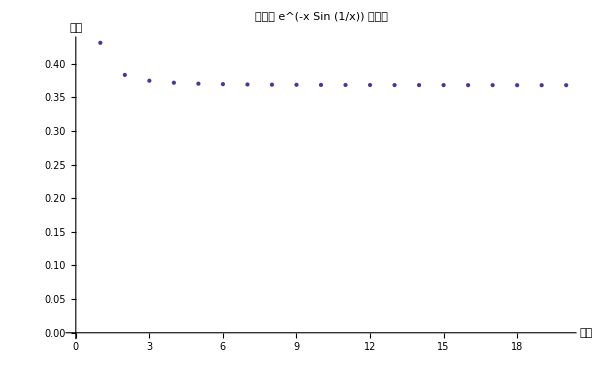
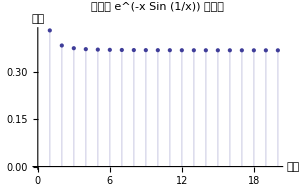
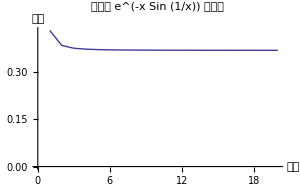

```mathematica
example4=Table[exampleSeries4,{n,1,20}];
Grid[{
{ListPlot[example4,GridLines->{{},{1}},PlotLabel->"通项为 e^(-x Sin (1/x)) 的数列",AxesLabel->{"项数","数列"},AxesStyle->Arrowheads[Automatic,Automatic],AxesOrigin->{0,0},PlotRange->Full,ImageSize->2imgSize]},
{ListPlot[example4,Filling->Axis,GridLines->{{},{1}},PlotLabel->"通项为 e^(-x Sin (1/x)) 的数列",AxesLabel->{"项数","数列"},AxesStyle->Arrowheads[Automatic,Automatic],AxesOrigin->{0,0},PlotRange->Full,ImageSize->imgSize]
ListPlot[example4,Joined->True,GridLines->{{},{1}},PlotLabel->"通项为 e^(-x Sin (1/x)) 的数列",AxesLabel->{"项数","数列"},AxesStyle->Arrowheads[Automatic,Automatic],AxesOrigin->{0,0},PlotRange->Full,ImageSize->imgSize]}
}]
```

```mathematica
Limit[Exp[-n Sin[1/n]],n->Infinity]
```

1/ⅇ

有一点要很小心，即这个数量通项写出来虽然是一个递减的，然而这个通项所对应的连续自变量的函数却是个振荡的。

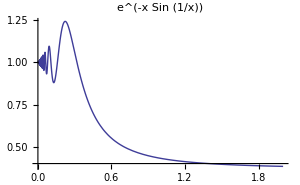

```mathematica
Plot[Exp[-x Sin[1/x]],{x,0,2},ImageSize->imgSize,PlotLabel->"e^(-x Sin (1/x))"]
```

这是一个有警示性的例子。有时候我们找了几个自变量，算了函数值，然后我们就武断的给出了函数是个单调性等性质，看看这个例子的情况，我们就知道有时候是必须很小心的。

#### 其他情形

当然还用其他的情形。比如函数一直保持在某值下方，但是却震荡着接近该值等等。还用趋于无穷的各种情况。

### 数项级数收敛

级数是否收敛，需要判断级数和随项数的变化趋势。我们有各种准则来判断，不过我们这里不是来讨论准则的，而是来看图的。

#### 关于收敛的简单例子

调和级数是一个很经典的级数。

```mathematica
Append[Table[1/n,{n,1,10}],"..."]
```

{1,1/2,1/3,1/4,1/5,1/6,1/7,1/8,1/9,1/10,...}

```mathematica
harmonicNumber[n_]=Sum[1/i,{i,1,n}]
```

HarmonicNumber[n]

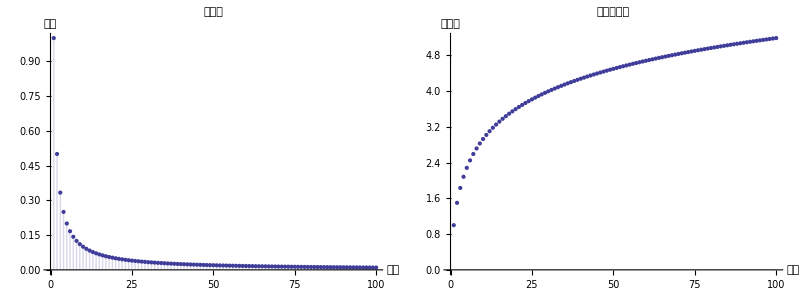

```mathematica
Grid[{
{ListPlot[Table[1/n,{n,1,100}],Filling->Axis,PlotLabel->"调和数",AxesLabel->{"项数","数列"},AxesStyle->Arrowheads[Automatic,Automatic],AxesOrigin->{0,0},PlotRange->Full,ImageSize->imgSize],
ListPlot[Table[harmonicNumber[n],{n,1,100}],PlotLabel->"调和级数和",AxesLabel->{"项数","级数和"},AxesStyle->Arrowheads[Automatic,Automatic],AxesOrigin->{0,0},PlotRange->Full,ImageSize->imgSize]}
}]
```

继续往后画，可以发现级数和依然没有停止增长的趋势，实际上调和级数是发散的：

```mathematica
Limit[harmonicNumber[n],{n->Infinity}]
```

{∞}

上面在画调和级数的图像的时候，我为什么要把线条下面加竖线阴影呢？级数和是什么意思？就是我所画的这些数值的线段的长度加起来。或者，一个更好的理解方法是，我们把左边的那个画成 BarChart，如下图

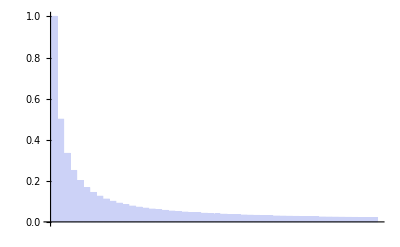

```mathematica
BarChart[Table[1/n,{n,1,50}]]
```

我们可以认为级数和就是这些竖条的面积，因为这些竖条的宽都是 1 。也就是说，虽然随着 n 增大，每项的值越来越小，但是还是减小的不够快（看上面调和级数和的图和级数和极限的结果）。

我们稍微改动一下，把原来通项的分母上的 n 换成 n^2 。这样我们再看看。

```mathematica
harmonicNumber2[n_]=Sum[1/i^2,{i,1,n}]
```

HarmonicNumber[n,2]

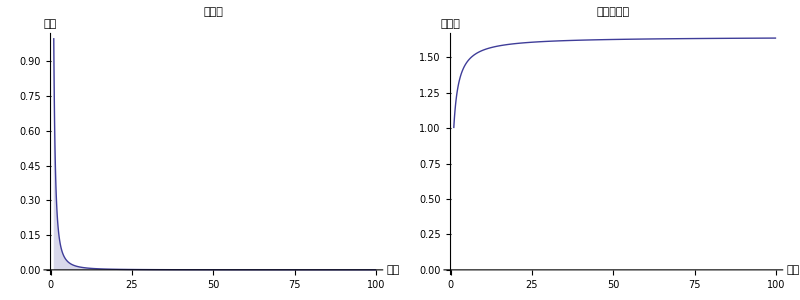

```mathematica
Grid[{
{Plot[1/n^2,{n,1,100},Filling->Axis,PlotLabel->"调和数",AxesLabel->{"项数","数列"},AxesStyle->Arrowheads[Automatic,Automatic],AxesOrigin->{0,0},PlotRange->Full,ImageSize->imgSize],
Plot[harmonicNumber2[n],{n,1,100},PlotLabel->"调和级数和",AxesLabel->{"项数","级数和"},AxesStyle->Arrowheads[Automatic,Automatic],AxesOrigin->{0,0},PlotRange->Full,ImageSize->imgSize]}
}]
```

改过之后的级数随着项数的增加减小的更快了。从右侧的级数和的情况来看，有希望是一个收敛的。我们来验证一下：

```mathematica
Limit[Sum[1/i^2,{i,1,n}],{n->Infinity}]
```

{π^2/6}

果然是收敛的。也就是说当我们让第一个调和级数减小速度的更快之后，有可能获得一个收敛的级数。

这两个例子也告诉我们，虽然调和级数只看左边的级数分布的图似乎是与横轴所夹面积是收敛的（毕竟单调减少嘛），但是我们不能看看这个图就下结论，而且实际上上面证明我们的感觉是错的。所以我们需要一些定理一些准则来帮助我们做收敛判断。

#### 条件收敛的例子

如果我们的级数 An 是收敛的，但是 |An| 级数却不收敛，那么我们就说这是条件收敛。

我们拿莱布尼兹级数来做例子。各个项为：

```mathematica
Append[Table[(-1)^(n+1)1/n,{n,1,10}],"..."]
```

{1,-1/2,1/3,-1/4,1/5,-1/6,1/7,-1/8,1/9,-1/10,...}

级数为

```mathematica
lbnz[n_]=Sum[(-1)^(x+1)1/x,{x,1,n}]
```

-(-1)^n LerchPhi[-1,1,1+n]+Log[2]

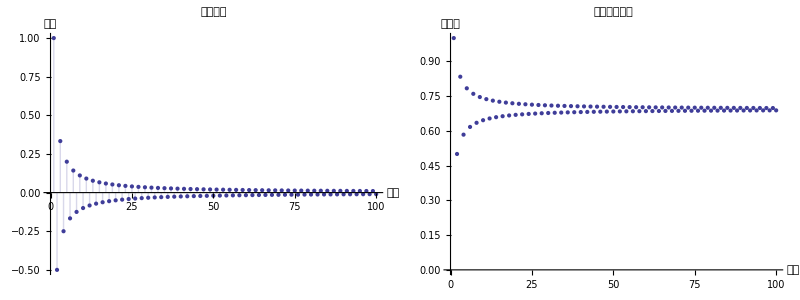

```mathematica
Grid[{
{ListPlot[Table[(-1)^(n+1)1/n,{n,1,100}],Filling->Axis,PlotLabel->"莱布尼兹",AxesLabel->{"项数","数列"},AxesStyle->Arrowheads[Automatic,Automatic],AxesOrigin->{0,0},PlotRange->Full,ImageSize->imgSize],
ListPlot[Table[lbnz[n],{n,1,100}],PlotLabel->"莱布尼兹级数",AxesLabel->{"项数","级数和"},AxesStyle->Arrowheads[Automatic,Automatic],AxesOrigin->{0,0},PlotRange->Full,ImageSize->imgSize]}
}]
```

看起来是收敛的，我们证明一下：

```mathematica
Limit[lbnz[n],n->Infinity]
```

Log[2]

确实是收敛的。

而莱布尼兹级数如果每项加绝对值，就变成了调和级数，我们前面证明了调和级数不收敛。所以莱布尼兹级数其实是条件收敛的。

### 函数级数

除了数项级数，我们还有函数级数。函数级数是一个很重要的概念，因为这会涉及到我们后面很多的内容。

一个简单的函数级数的项的例子是：

```mathematica
Append[Table[x^(n-1)-x^n,{n,1,10}],"..."]
```

{1-x,x-x^2,x^2-x^3,x^3-x^4,x^4-x^5,x^5-x^6,x^6-x^7,x^7-x^8,x^8-x^9,x^9-x^10,...}

相应的级数（和）是：

```mathematica
funcSeries[x_,n_]=Sum[x^(i-1)-x^i,{i,1,n}]
```

1-x^n

```mathematica
Table[funcSeries[x,n],{n,1,5}]
```

{1-x,1-x^2,1-x^3,1-x^4,1-x^5}

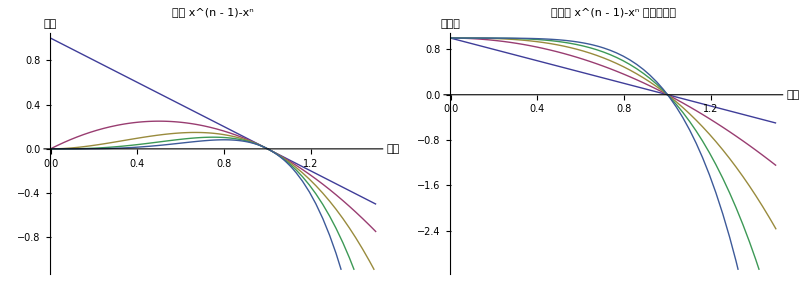

```mathematica
Grid[{
{Plot[Evaluate@Table[x^(n-1)-x^n,{n,1,5}],{x,0,1.5},PlotLabel->"通项 x^(n - 1)-x^n",AxesLabel->{"项数","通项"},AxesStyle->Arrowheads[Automatic,Automatic],AxesOrigin->{0,0},ImageSize->imgSize],
Plot[Evaluate@Table[funcSeries[x,n],{n,1,5}],{x,0,1.5},PlotLabel->"通项为 x^(n - 1)-x^n 的函数级数",AxesLabel->{"项数","级数和"},AxesStyle->Arrowheads[Automatic,Automatic],ImageSize->imgSize]}
}]
```

左边是各个通项，随着 n 的增加，通项函数值越来越小；右边是级数的情况，随着 n 的增加，级数在 (0,1) 部分都是限制在 1 以下的，但是在 (1,Infinity) 范围内看起来却没有下限。

我们来验证上面的直观印象：

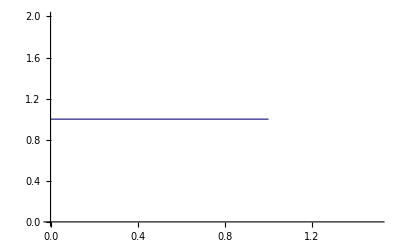

```mathematica
Plot[Limit[funcSeries[x,n],n->Infinity],{x,0,1.5},PlotStyle->Thick]
```

在上面的线段的端点上看不出来，我们单独给个数字：

在 x=1 点：

```mathematica
Limit[funcSeries[1,n],n->Infinity]
```

0

在 x=0 点：

```mathematica
Limit[funcSeries[0,n],n->Infinity]
```

1

为什么 x>1 的部分没有显示？我们釆点看看。取 x 为 {1.1,1.2,1.3,1.4,1.5,1.6}几个点：

```mathematica
Table[Limit[funcSeries[x,n],n->Infinity],{x,{1.1,1.2,1.3,1.4,1.5,1.6}}]
```

{-∞,-∞,-∞,-∞,-∞,-∞}

有种很重要的幂级数是幂级数。我们前面看了莱布尼兹级数，就是以 1/n x^n 幂级数的一种特殊情况（x=-1）

这个特殊的幂级数通项：

```mathematica
Append[Table[1/n x^n,{n,1,10}],"..."]
```

{x,x^2/2,x^3/3,x^4/4,x^5/5,x^6/6,x^7/7,x^8/8,x^9/9,x^10/10,...}

明显当 x=-1 时就变成莱布尼兹级数通项了。

幂级数里面有个阿贝尔定理，说的是如果幂级数在 x=r>0 时收敛，那么幂级数在区间 [0,r] 上一致收敛。我们通过例子来形象的看看这个定理。通项：

```mathematica
Table[(-1)^n 1/n x^n,{n,1,10}]
```

{-x,x^2/2,-x^3/3,x^4/4,-x^5/5,x^6/6,-x^7/7,x^8/8,-x^9/9,x^10/10}

级数和

```mathematica
funcSeriesAbTh[x_,n_]=Sum[(-1)^i 1/i x^i,{i,1,n}]
```

(-x)^n x LerchPhi[-x,1,1+n]-Log[1+x]

这个级数在 x=1 时的极限：

```mathematica
Limit[funcSeriesAbTh[1,n],n->Infinity]
```

-Log[2]

那么按照阿贝尔定理，我们的这个幂级数在 [0,1] 上一致收敛的。

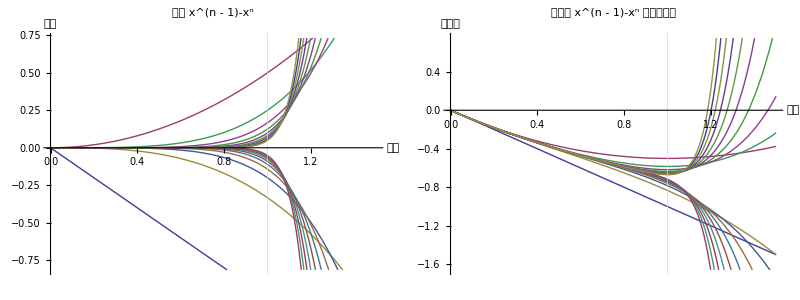

```mathematica
Grid[{
{Plot[Evaluate@Table[(-1)^n 1/n x^n,{n,1,20}],{x,0,1.5},GridLines->{{1},{}},PlotLabel->"通项 x^(n - 1)-x^n",AxesLabel->{"项数","通项"},AxesStyle->Arrowheads[Automatic,Automatic],AxesOrigin->{0,0},ImageSize->imgSize],
Plot[Evaluate@Table[funcSeriesAbTh[x,n],{n,1,20}],{x,0,1.5},GridLines->{{1},{}},PlotLabel->"通项为 x^(n - 1)-x^n 的函数级数",AxesLabel->{"项数","级数和"},ImageSize->imgSize]}
}]
```

看起来是在 (0,1) 收敛的。这个级数和在 0<=x<=1 时是递增的，如果在 x=1 处收敛，那么在 [0,1] 上也是收敛的，而且是一致收敛（需证明，直观的请看下图，绘制了 100 项到 109 项。）。

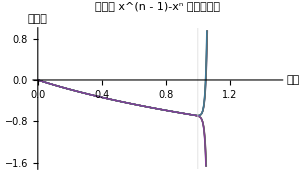

```mathematica
Plot[Evaluate@Table[funcSeriesAbTh[x,n],{n,100,109}],{x,0,1.5},GridLines->{{1},{}},PlotLabel->"通项为 x^(n - 1)-x^n 的函数级数",AxesLabel->{"项数","级数和"},ImageSize->imgSize]
```